```mathematica
Ejemplos de Mathematica
```

```mathematica
Problema 1
```

```mathematica
getRed[ec1_,ec2_,num_,arg_]:=
If[num == 1,
Reduce[ec1,arg,Reals],
Reduce[ec2,arg,Reals]
]
```

```mathematica
getRed[(5x+y == 8),(3x-y==8),2,y]
```

y==-8+3 x

```mathematica
Método de sustitución.
```

```mathematica
sust[ec1_,ec2_,num_,arg_]:=(
res= getRed[ec1,ec2,num,arg];
reduced = res[[2]];
replaced = ReplaceAll[ec2,arg-> reduced];
incog1 = Reduce[replaced];
Print[incog1];
arg2 = incog1[[1]];
incog2 = Reduce[ReplaceAll[ec2,arg2->incog1[[2]]]];
Print[incog2];
If[arg==x,
p = Point[{incog2[[2]],incog1[[2]]}],
p = Point[{incog1[[2]],incog2[[2]]}]
];
Plot[{Reduce[ec1,y][[2]], Reduce[ec2,y][[2]]},{x,-10,10},Epilog->{Black,AbsolutePointSize[5],p}]
)
```

x==2

y==-2

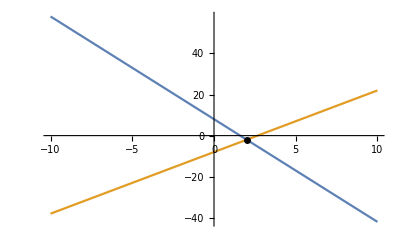

```mathematica
sust[(5x+y == 8),(3x-y==8),1,y]
```

```mathematica
Método de reducción
```

```mathematica
reduct[ec1_,ec2_]:=(
x1 = ec1[[1]][[1]][[1]];(*Toma el primer valor*)
x2 = ec2[[1]][[1]][[1]];
y1 = ec1[[1]][[2]][[1]];
y2 = ec2[[1]][[2]][[1]];
v1= ec1[[-1]];(*Ultimo*)
v2 = ec2[[-1]];

nx1=x1*x2;
ny1=y1*x2;
nv1=v1*x2;

nx2=x2*x1;
ny2=y2*x1;
nv2=v2*x1;

func = Function[{u,v},((nx1-nx2)u+(ny1-ny2)v)==(nv1-nv2)][x,y];
reduced=Reduce[func];
rx = ReplaceAll[ec1,y->reduced[[2]]];
redurx= Reduce[rx];
Print[redurx];
Print[reduced];
Plot[{Reduce[ec1,y][[2]], Reduce[ec2,y][[2]]},{x,-10,10},Epilog->{Black,AbsolutePointSize[5],Point[{redurx[[2]],reduced[[2]]}]}]
)
```

x==2

y==1

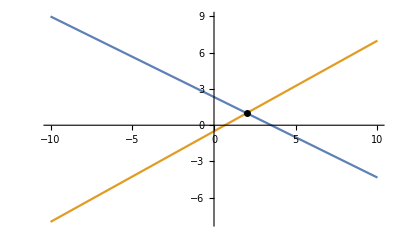

```mathematica
reduct[(2x+3y==7),(-3x+4y==-2)]
```

```mathematica
Método de igualación.
```

```mathematica
igualación[ec1_,ec2_,arg_]:=(
reduce1=Reduce[ec1,arg,Reals];
reduce2=Reduce[ec2,arg,Reals];
replaced = ReplaceAll[reduce1, arg->reduce2[[2]]];
incog1 = Reduce[replaced];
Print[incog1];
arg2 = incog1[[1]];
incog2 = Reduce[ReplaceAll[ec2,arg2->incog1[[2]]]];
Print[incog2];
If[arg==x,
p = Point[{incog2[[2]],incog1[[2]]}],
p = Point[{incog1[[2]],incog2[[2]]}]
];
Plot[{Reduce[ec1,y][[2]], Reduce[ec2,y][[2]]},{x,-10,10},Epilog->{Black,AbsolutePointSize[5],p}]
)
```

y==-2

x==1

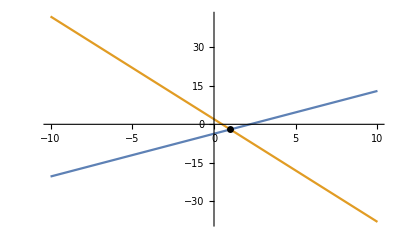

```mathematica
igualación[(5x-3y==11),(4x+y==2),x]
```

```mathematica
Método de Crammer
```

```mathematica
crammer[ec1_,ec2_]:=(
x1=ec1[[1]][[1]][[1]];
x2=ec2[[1]][[1]][[1]];
y1=ec1[[1]][[2]][[1]];
y2=ec2[[1]][[2]][[1]];
ti1=ec1[[-1]];
ti2=ec2[[-1]];
determinanteS = (x1*y2)-(x2*y1);
determinanteX =(ti1*y2)-(ti2*y1);
determinanteY =(x1*ti2)-(x2*ti1);
incog1=Function[{u},u==(determinanteX/determinanteS)][x];
Print[incog1];
incog2=Function[{v},v==determinanteY/determinanteS][y];
Print[incog2];
Plot[{Reduce[ec1,y][[2]], Reduce[ec2,y][[2]]},{x,-10,10},Epilog->{Black,AbsolutePointSize[5],Point[{incog1[[2]],incog2[[2]]}]}]
)
```

x==-2

y==-4

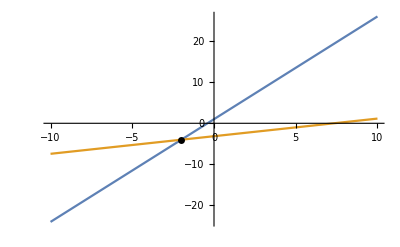

```mathematica
crammer[(5x-2y==-2),(-3x+7y==-22)]
```

```mathematica
general[ec1_,ec2_,arg_,metodo_]:=(
Which[metodo==1, sust[ec1,ec2,1,arg],
	metodo==2,reduct[ec1,ec2],
	metodo==3,igualacion[ec1,ec2,arg],
	metodo==4, crammer[ec1,ec2]
];
)
```

```mathematica
general[(5x-2y==-2),(-3x+7y==-22),x,2]
```